# Classifications, predictions, and recommendations with features

## Wednesday

Anton Antonov
Digital Humanities at Oxford Summer School 2017
July 2017

## Introduction

This notebook shows the making of a classifier using image keypoints.

Here are the steps.

Get a collection of images; (“CIFAR-10”).

And split into training and testing data sets.

Compute image keypoints descriptors for each image.

Cluster the descriptors into 100 clusters.

Find the mean descriptor of each cluster.

For each image make a profile that is the number of image’s descriptors that belong to each of the clusters.

Make a classifier over the descriptor clusters profiles.

Evaluate the classifier.

Remark: Instead of profiles based on cluster membership (or proximity) we can use profiles derived from dimension reduction.

## ImageKeypoints Applications example

Object recognition using "bag of words" on a dataset of 5,000 images 32×32 each, belonging to 10 categories:

```mathematica
obj=ResourceObject["CIFAR-10"];
training=ResourceData[obj,"TrainingData"];
testing=Flatten[Table[training[[i+1000;;i+1099]],{i,1,50000,5000}]];training=Flatten[Table[training[[i;;i+499]],{i,1,50000,5000}]];
```

```mathematica
Length[training]
```

5000

```mathematica
Length[testing]
```

1000

Compute keypoint descriptors on 256×256 images and create the codebook of visual words:

```mathematica
AbsoluteTiming[
kp=ParallelTable[
ImageKeypoints[ImageResize[i,256],"Descriptor"],{i,training[[All,1]]}
];]
```

{33.0801,Null}

```mathematica
Length@ImageKeypoints[ImageResize[training[[1332,1]],256],"Descriptor"]
```

203

```mathematica
Dimensions[kp⟦1⟧]
```

{113,64}

The codebook contains all image descriptors of length 64:

```mathematica
codebook=Flatten[kp,1];
Dimensions[codebook]
```

{698180,64}

```mathematica
RecordsSummary[codebook]
AutoCollapse[]
```

{1 column 1
Min | -0.60604
1st Qu | -0.0247273
Median | 0.000572773
Mean | 0.00618047
3rd Qu | 0.0282997
Max | 0.66819,2 column 2
Min | -0.608252
1st Qu | -0.0185871
Median | 0.0132658
Mean | 0.0268848
3rd Qu | 0.0620977
Max | 0.693392,3 column 3
Min | 0.
1st Qu | 0.0287722
Median | 0.056733
Mean | 0.0730732
3rd Qu | 0.0967237
Max | 0.902943,4 column 4
Min | 0.
1st Qu | 0.0433043
Median | 0.0769408
Mean | 0.0954595
3rd Qu | 0.124815
Max | 0.918779,5 column 5
Min | -0.444406
1st Qu | -0.0354483
Mean | -0.00214193
Median | -0.000678598
3rd Qu | 0.0304838
Max | 0.430871,6 column 6
Min | -0.643144
1st Qu | -0.0373411
Median | 0.0155117
Mean | 0.0329373
3rd Qu | 0.0916132
Max | 0.578089,7 column 7
Min | 0.
1st Qu | 0.0401864
Median | 0.0771685
Mean | 0.0891486
3rd Qu | 0.124441
Max | 0.630778,8 column 8
Min | 0.
1st Qu | 0.070722
Median | 0.123315
Mean | 0.145441
3rd Qu | 0.195545
Max | 0.74837,9 column 9
Min | -0.440137
1st Qu | -0.0303168
Median | 0.000888841
Mean | 0.00259514
3rd Qu | 0.0367644
Max | 0.474423,10 column 10
Min | -0.566724
1st Qu | -0.0368701
Median | 0.0158276
Mean | 0.0333304
3rd Qu | 0.0919067
Max | 0.604582,11 column 11
Min | 0.
1st Qu | 0.0402222
Median | 0.0776643
Mean | 0.0902251
3rd Qu | 0.125856
Max | 0.594404,12 column 12
Min | 0.
1st Qu | 0.0706511
Median | 0.123255
Mean | 0.145357
3rd Qu | 0.195218
Max | 0.807978,13 column 13
Min | -0.704758
1st Qu | -0.0288841
Mean | -0.00654751
Median | -0.000688909
3rd Qu | 0.0247224
Max | 0.581287,14 column 14
Min | -0.549607
1st Qu | -0.0181414
Median | 0.0133175
Mean | 0.0268668
3rd Qu | 0.0615925
Max | 0.675247,15 column 15
Min | 0.
1st Qu | 0.02854
Median | 0.0564823
Mean | 0.0729736
3rd Qu | 0.0966902
Max | 0.777592,16 column 16
Min | 0.
1st Qu | 0.0427259
Median | 0.0762884
Mean | 0.0948981
3rd Qu | 0.124214
Max | 0.869398,17 column 17
Min | -0.542024
1st Qu | -0.0320124
Median | 0.00136726
Mean | 0.00938971
3rd Qu | 0.0412441
Max | 0.613786,18 column 18
Min | -0.394252
1st Qu | -0.000769912
Median | 0.0407087
Mean | 0.0497378
3rd Qu | 0.101886
Max | 0.47892,19 column 19
Min | 0.
1st Qu | 0.0427185
Median | 0.0842332
Mean | 0.102084
3rd Qu | 0.139529
Max | 0.819737,20 column 20
Min | 0.
1st Qu | 0.0703523
Median | 0.115111
Mean | 0.121984
3rd Qu | 0.165443
Max | 0.580804,21 column 21
Min | -0.405852
1st Qu | -0.0282316
Mean | -0.00308116
Median | -0.000364255
3rd Qu | 0.024108
Max | 0.37034,22 column 22
Min | -0.330081
1st Qu | 0.017611
Median | 0.0818644
Mean | 0.0923087
3rd Qu | 0.162656
Max | 0.472231,23 column 23
Min | 0.
1st Qu | 0.0472779
Median | 0.0908426
Mean | 0.1012
3rd Qu | 0.143704
Max | 0.546207,24 column 24
Min | 0.
1st Qu | 0.115111
Median | 0.184248
Mean | 0.18818
3rd Qu | 0.254906
Max | 0.675007,25 column 25
Min | -0.423408
1st Qu | -0.0255031
Median | 0.000626595
Mean | 0.00383375
3rd Qu | 0.0316302
Max | 0.418261,26 column 26
Min | -0.342843
1st Qu | 0.0168065
Median | 0.0805467
Mean | 0.0914481
3rd Qu | 0.16164
Max | 0.460084,27 column 27
Min | 0.
1st Qu | 0.0478729
Median | 0.0927644
Mean | 0.103878
3rd Qu | 0.147487
Max | 0.54377,28 column 28
Min | 0.
1st Qu | 0.114144
Median | 0.18227
Mean | 0.186249
3rd Qu | 0.252244
Max | 0.667794,29 column 29
Min | -0.56229
1st Qu | -0.0430924
Mean | -0.0105457
Median | -0.00152873
3rd Qu | 0.0325564
Max | 0.568975,30 column 30
Min | -0.415478
1st Qu | -0.00207667
Median | 0.039307
Mean | 0.0484437
3rd Qu | 0.101101
Max | 0.430005,31 column 31
Min | 0.
1st Qu | 0.0428365
Median | 0.0847246
Mean | 0.103725
3rd Qu | 0.141254
Max | 0.8421,32 column 32
Min | 0.
1st Qu | 0.06976
Median | 0.11465
Mean | 0.121907
3rd Qu | 0.165864
Max | 0.59477,33 column 33
Min | -0.557422
1st Qu | -0.014813
Median | 0.0109251
Mean | 0.0279582
3rd Qu | 0.0639049
Max | 0.596821,34 column 34
Min | -0.414839
1st Qu | -0.011163
Median | 0.0285977
Mean | 0.0364892
3rd Qu | 0.0909165
Max | 0.472148,35 column 35
Min | 0.
1st Qu | 0.0424266
Median | 0.086383
Mean | 0.104359
3rd Qu | 0.144499
Max | 0.863511,36 column 36
Min | 0.
1st Qu | 0.0673951
Median | 0.114648
Mean | 0.121936
3rd Qu | 0.16785
Max | 0.625803,37 column 37
Min | -0.334962
1st Qu | -0.0190202
Median | 0.0037983
Mean | 0.0101867
3rd Qu | 0.0386677
Max | 0.382177,38 column 38
Min | -0.452131
1st Qu | 0.00541156
Median | 0.0681081
Mean | 0.0817553
3rd Qu | 0.157001
Max | 0.47366,39 column 39
Min | 0.
1st Qu | 0.0468672
Median | 0.0929256
Mean | 0.104081
3rd Qu | 0.149211
Max | 0.550584,40 column 40
Min | 0.
1st Qu | 0.109379
Median | 0.184854
Mean | 0.188414
3rd Qu | 0.260317
Max | 0.71987,41 column 41
Min | -0.445977
1st Qu | -0.0424285
Mean | -0.0121666
Median | -0.0041501
3rd Qu | 0.0200388
Max | 0.358012,42 column 42
Min | -0.44959
1st Qu | 0.00447754
Median | 0.0666808
Mean | 0.080359
3rd Qu | 0.156119
Max | 0.466465,43 column 43
Min | 0.
1st Qu | 0.047585
Median | 0.0946243
Mean | 0.106978
3rd Qu | 0.153146
Max | 0.552124,44 column 44
Min | 0.
1st Qu | 0.108566
Median | 0.182972
Mean | 0.186731
3rd Qu | 0.258107
Max | 0.682222,45 column 45
Min | -0.585582
1st Qu | -0.0654941
Mean | -0.0286729
Median | -0.0108562
3rd Qu | 0.0157267
Max | 0.561283,46 column 46
Min | -0.439376
1st Qu | -0.0129404
Median | 0.0276674
Mean | 0.0350557
3rd Qu | 0.0904057
Max | 0.466491,47 column 47
Min | 0.
1st Qu | 0.0427449
Median | 0.0870528
Mean | 0.106
3rd Qu | 0.146274
Max | 0.67975,48 column 48
Min | 0.
1st Qu | 0.0672264
Median | 0.114437
Mean | 0.121875
3rd Qu | 0.167612
Max | 0.68199,49 column 49
Min | -0.598638
1st Qu | -0.0101638
Median | 0.00938868
Mean | 0.0220352
3rd Qu | 0.0472949
Max | 0.687266,50 column 50
Min | -0.681853
1st Qu | -0.0480393
Mean | -0.0112972
Median | -0.00204661
3rd Qu | 0.0311832
Max | 0.63093,51 column 51
Min | 0.
1st Qu | 0.0291512
Median | 0.0588266
Mean | 0.0748164
3rd Qu | 0.100374
Max | 0.874371,52 column 52
Min | 0.
1st Qu | 0.0416027
Median | 0.0764566
Mean | 0.0932501
3rd Qu | 0.124324
Max | 0.778205,53 column 53
Min | -0.418576
1st Qu | -0.024376
Median | 0.00411168
Mean | 0.0113724
3rd Qu | 0.0457457
Max | 0.458117,54 column 54
Min | -0.586118
1st Qu | -0.0834867
Mean | -0.0200715
Median | -0.0047087
3rd Qu | 0.0450446
Max | 0.615269,55 column 55
Min | 0.
1st Qu | 0.0401861
Median | 0.080497
Mean | 0.0925257
3rd Qu | 0.130932
Max | 0.643973,56 column 56
Min | 0.
1st Qu | 0.0681687
Median | 0.125239
Mean | 0.14432
3rd Qu | 0.198964
Max | 0.790439,57 column 57
Min | -0.472984
1st Qu | -0.0475473
Mean | -0.0131625
Median | -0.00450119
3rd Qu | 0.0238751
Max | 0.445892,58 column 58
Min | -0.614697
1st Qu | -0.0834416
Mean | -0.0198378
Median | -0.00457657
3rd Qu | 0.0453132
Max | 0.619502,59 column 59
Min | 0.
1st Qu | 0.0402029
Median | 0.0809465
Mean | 0.0936355
3rd Qu | 0.132111
Max | 0.717966,60 column 60
Min | 0.
1st Qu | 0.0681998
Median | 0.125325
Mean | 0.144123
3rd Qu | 0.198211
Max | 0.765099,61 column 61
Min | -0.698547
1st Qu | -0.0477506
Mean | -0.0224121
Median | -0.00934701
3rd Qu | 0.0103218
Max | 0.656539,62 column 62
Min | -0.694846
1st Qu | -0.0469947
Mean | -0.0108269
Median | -0.00182498
3rd Qu | 0.0317825
Max | 0.619535,63 column 63
Min | 0.
1st Qu | 0.0288409
Median | 0.0586204
Mean | 0.0750983
3rd Qu | 0.100745
Max | 0.826538,64 column 64
Min | 0.
1st Qu | 0.0411853
Median | 0.0759472
Mean | 0.0927329
3rd Qu | 0.123587
Max | 0.787937}

Find 100 visual codewords using k-means clustering:

```mathematica
AbsoluteTiming[
clust=ClusteringComponents[codebook,100,1,Method->"KMeans",PerformanceGoal->"Speed"];]
```

{296.813,Null}

This finds the mean point of each cluster.

```mathematica
codewords=Table[
p=Flatten@Position[clust,i];
Mean[codebook[[p]]],
{i,Max@clust}];
```

Image features are defined as the normalized counts of all the codewords:

```mathematica
nf=Nearest[codewords->Automatic];
```

```mathematica
imageCodewordsFeatureExtract[image_?ImageQ]:=imageCodewordsFeatureExtract[ImageKeypoints[ImageResize[image,{256,256}],"Descriptor"]];
imageCodewordsFeatureExtract[keypoints_List]:=Module[
{h},
h=N@BinCounts[First@nf[#,1] &/@keypoints, {1,Length@codewords+1}];
h/Total[h]
];
```

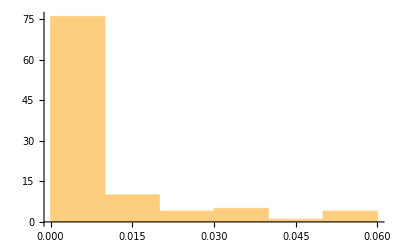

```mathematica
imageCodewordsFeatureExtract[RandomSample[training][[1,1]]]//Histogram
```

Construct a classifier trained on extracted image features:

```mathematica
t=Table[imageCodewordsFeatureExtract[kp[[i]]]->training[[i,2]],
{i,Length@training}];
```

```mathematica
classifier=Classify[t];
```

Evaluate the classifier on test data:

```mathematica
cm=ClassifierMeasurements[classifier,Table[imageCodewordsFeatureExtract[First@sample]->Last@sample,{sample,testing}]];
```

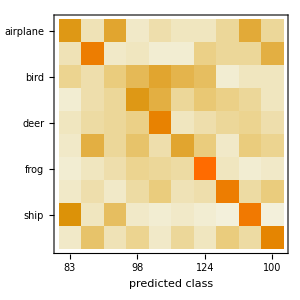

```mathematica
cm["ConfusionMatrixPlot"]
```